Optimal control for generating coherent states and readout

Clear the environment

```mathematica
ClearAll["Global`*"];
```

Parameter assumptions

```mathematica
$Assumptions={ω∈Reals,χ∈Reals,κ∈Reals&&κ≥0,t∈Reals&&t≥0,s∈Reals&&s≥0,Ω∈Reals,x[t]∈Reals,p[t]∈Reals,x'[t]∈Reals,p'[t]∈Reals,ϵ1[t]∈Reals,ϵ2[t]∈Reals,α∈Reals,β∈Reals,σ∈Reals};
```

Langevin Equation

```mathematica
Le[t_,χ_,κ_,σ_]=D[a[t],t]+I*χ*σ*a[t]+κ/2*a[t]+Ω[t];
TraditionalForm[Le[t,χ,κ,σ]]
```

a'(t)+1/2 κ a(t)+ⅈ σ χ a(t)+Ω(t)

Separate in Real and imaginary part

```mathematica
LeRI[t_,χ_,κ_,σ_]=Le[t,χ,κ,σ]/.{a[t]->x[t]+I*p[t],a'[t]->x'[t]+I*p'[t],Ω[t]->ϵ1[t]+I*ϵ2[t]};
TraditionalForm[LeRI[t,χ,κ,σ]]
```

ⅈ p'(t)+1/2 κ (x(t)+ⅈ p(t))+ⅈ σ χ (x(t)+ⅈ p(t))+x'(t)+ϵ1(t)+ⅈ ϵ2(t)

Write the differential equation as a linear system

```mathematica
X[t_]={x[t],p[t]};
```

```mathematica
u[t_]={ϵ1[t],ϵ2[t]};
```

```mathematica
A=-{Grad[FullSimplify[Re[LeRI[t,χ,κ,σ]]],X[t]],Grad[FullSimplify[Im[LeRI[t,χ,κ,σ]]],X[t]]};
TraditionalForm[A]
```

(-κ/2 | σ χ
-σ χ | -κ/2)

```mathematica
B=-{Grad[FullSimplify[Re[LeRI[t,χ,κ,σ]]],u[t]],Grad[FullSimplify[Im[LeRI[t,χ,κ,σ]]],u[t]]};
TraditionalForm[B]
```

(-1 | 0
0 | -1)

Optimal control Pulse

```mathematica
Xf={α,β};
X0={0,0};
```

```mathematica
μ1=FullSimplify[Inverse[Integrate[MatrixExp[A*(s-t)].B.Transpose[B].Transpose[MatrixExp[A*(s-t)]],{t,0,s}]]];
TraditionalForm[μ1]
```

(κ (1/(ⅇ^(κ s)-1)+1) | 0
0 | κ (1/(ⅇ^(κ s)-1)+1))

```mathematica
μ2=(Xf-MatrixExp[A*s].X0);
```

```mathematica
μ=FullSimplify[μ1.μ2];
```

```mathematica
uopt[t_,s_,χ_,κ_,σ_,α_,β_]=FullSimplify[2*Transpose[B].Transpose[MatrixExp[A*(s-t)]].μ];
TraditionalForm[uopt[t,s,χ,κ,σ,α,β]]
```

{-(2 κ ⅇ^(1/2 κ (s+t)) (α cos(σ χ (s-t))-β sin(σ χ (s-t))))/(ⅇ^(κ s)-1),-(2 κ ⅇ^(1/2 κ (s+t)) (α sin(σ χ (s-t))+β cos(σ χ (s-t))))/(ⅇ^(κ s)-1)}

Solve the Langevin Equation for two different pulses and find the weights such that both gives the same drive amplitude

```mathematica
Leopt[t_,s_,χ_,κ_,σ_,α_,β_]=Le[t,χ,κ,σ]/.{Ω[t]->uopt[t,s,χ,κ,σ,α,β][[1]]+I*uopt[t,s,χ,κ,σ,α,β][[2]]};
```

```mathematica
Solopt[t_,s_,χ_,κ_,σ_,α_,β_]=FullSimplify[DSolve[{Leopt[t,s,χ,κ,σ,α,β]==0,a[0]==0},a[t],t]]
```

{{a[t]→(2 ⅇ^(1/2 (s-t) (κ+2 ⅈ σ χ)) (-1+ⅇ^(t κ)) (α+ⅈ β))/(-1+ⅇ^(s κ))}}

```mathematica
Calopt1a=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==Im[af]},{α,β},Reals]]
Calopt1b=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==Im[af]},{α,β},Reals]]
```

{{α→-0.623416,β→4.96098}}

{{α→-0.623416,β→4.96098}}

```mathematica
Calopt2a=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==10*Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==10*Im[af]},{α,β},Reals]]
Calopt2b=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==10*Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==10*Im[af]},{α,β},Reals]]
```

{{α→-6.23416,β→49.6098}}

{{α→-6.23416,β→49.6098}}

```mathematica
Calopt3a=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==100*Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,1,α,β][[1,1,2]]]]==100*Im[af]},{α,β},Reals]]
Calopt3b=N[Solve[{FullSimplify[Re[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==100*Re[af],FullSimplify[Im[Solopt[10,10,0.25,2*π*0.01,-1,α,β][[1,1,2]]]]==100*Im[af]},{α,β},Reals]]
```

{{α→-62.3416,β→496.098}}

{{α→-62.3416,β→496.098}}

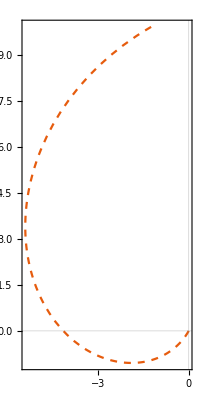

```mathematica
ParametricPlot[{{Re[Solopt[t,10,0.25,2*π*0.01,1,α,β][[1,1,2]]/.Calopt1a[[1]]],Im[Solopt[t,10,0.25,2*π*0.01,1,α,β][[1,1,2]]/.Calopt1a[[1]]]}(*,{Re[Solopt[t,15,0.025,2*π*0.01,1,α,0][[1,1,2]]/.Calopt2a[[1]]],Im[Solopt[t,15,0.025,2*π*0.01,1,α,0][[1,1,2]]/.Calopt2a[[1]]]}*)},{t,0,10},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotStyle->{ColorData[97],{ColorData[97],Dashed}},PlotTheme->"Scientific"]
```

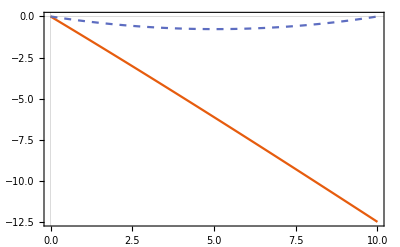

```mathematica
Plot[{Re[Solopt[t,10,0.025,2*π*0.01,1,α,0][[1,1,2]]/.Calopt2a[[1]]],Im[Solopt[t,10,0.025,2*π*0.01,1,α,0][[1,1,2]]/.Calopt2a[[1]]]},{t,0,10},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotStyle->{ColorData[97],{ColorData[97],Dashed}},PlotTheme->"Scientific"]
```

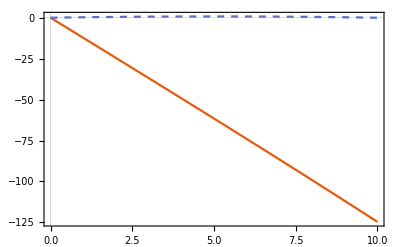

```mathematica
Plot[{Re[Solopt[t,10,0.0025,2*π*0.01,1,α,0][[1,1,2]]/.Calopt3a[[1]]],Im[Solopt[t,10,0.0025,2*π*0.01,-1,α,0][[1,1,2]]/.Calopt3a[[1]]]},{t,0,10},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotStyle->{ColorData[97],{ColorData[97],Dashed}},PlotTheme->"Scientific"]
```

Save data

```mathematica
CavityDisp1 = Table[Solopt[10/1000*i,10,0.25,2*π*0.01,1,α,β][[1,1,2]]/.Calopt1a[[1]],{i,0,1000}];
Export["CavityDisp1.csv",CavityDisp1];
```

```mathematica
CavityDisp2 = Table[Solopt[10/1000*i,10,0.025,2*π*0.01,1,α,β][[1,1,2]]/.Calopt2a[[1]],{i,0,1000}];
Export["CavityDisp2.csv",CavityDisp2];
```

```mathematica
CavityDisp3 = Table[Solopt[10/1000*i,10,0.0025,2*π*0.01,1,α,β][[1,1,2]]/.Calopt3a[[1]],{i,0,1000}];
Export["CavityDisp3.csv",CavityDisp3];
```

Signal To noise Ratio: Homodyne Operator

```mathematica
Hd[τ_,s_,χ_,κ_,σ_,α_,ϕ_]=κ*Integrate[Conjugate[Solopt[t,s,χ,κ,σ,α,0][[1,1,2]]]*Exp[I*ϕ]+Solopt[t,s,χ,κ,σ,α,0][[1,1,2]]*Exp[I*ϕ],{t,0,τ}]
```

-(16 ⅇ^((s κ)/2+ⅈ ϕ) α κ (κ Cos[s σ χ]-κ Cos[σ (s-τ) χ] Cosh[(κ τ)/2]+2 σ χ Sin[σ (s-τ) χ] Sinh[(κ τ)/2]))/((-1+ⅇ^(s κ)) (κ^2+4 σ^2 χ^2))

```mathematica
H2d[τ_,s_,χ_,κ_,σ_,α_,ϕ_]=TrigToExp[κ*τ+κ^2*Integrate[Conjugate[Solopt[t,s,χ,κ,σ,α,0][[1,1,2]]]*Conjugate[Solopt[x,s,χ,κ,σ,α,0][[1,1,2]]]*Exp[2*I*ϕ]+Solopt[t,s,χ,κ,σ,α,0][[1,1,2]]*Solopt[x,s,χ,κ,σ,α,0][[1,1,2]]*Exp[-2*I*ϕ]+2*Conjugate[Solopt[t,s,χ,κ,σ,α,0][[1,1,2]]]*Solopt[x,s,χ,κ,σ,α,0][[1,1,2]],{t,0,τ},{x,0,τ}]]
```

κ τ+1/((-1+ⅇ^(s κ))^2 (κ^2+4 σ^2 χ^2)^2)16 ⅇ^(s κ-κ τ-ⅈ (2 ϕ+σ (2 s+τ) χ)) α^2 κ^2 (4 ⅇ^(κ τ+4 ⅈ ϕ+ⅈ σ τ χ) κ^2+4 ⅇ^(κ τ+ⅈ σ (4 s+τ) χ) κ^2-4 ⅇ^((κ τ)/2+4 ⅈ s σ χ) κ (κ-2 ⅈ σ χ)-4 ⅇ^((3 κ τ)/2+4 ⅈ ϕ+2 ⅈ σ τ χ) κ (κ-2 ⅈ σ χ)-4 ⅇ^((κ τ)/2+2 ⅈ (ϕ+s σ χ)) κ (κ-2 ⅈ σ χ)-4 ⅇ^((3 κ τ)/2+2 ⅈ (ϕ+σ (s+τ) χ)) κ (κ-2 ⅈ σ χ)+ⅇ^(2 κ τ+4 ⅈ ϕ+3 ⅈ σ τ χ) (κ-2 ⅈ σ χ)^2-4 ⅇ^((3 κ τ)/2+4 ⅈ s σ χ) κ (κ+2 ⅈ σ χ)-4 ⅇ^((κ τ)/2+4 ⅈ ϕ+2 ⅈ σ τ χ) κ (κ+2 ⅈ σ χ)-4 ⅇ^((3 κ τ)/2+2 ⅈ (ϕ+s σ χ)) κ (κ+2 ⅈ σ χ)-4 ⅇ^((κ τ)/2+2 ⅈ (ϕ+σ (s+τ) χ)) κ (κ+2 ⅈ σ χ)+ⅇ^(2 κ τ+ⅈ σ (4 s-τ) χ) (κ+2 ⅈ σ χ)^2+ⅇ^(4 ⅈ ϕ+3 ⅈ σ τ χ) (κ+2 ⅈ σ χ)^2-ⅇ^(ⅈ σ (4 s-τ) χ) (ⅈ κ+2 σ χ)^2+4 ⅇ^(κ τ+2 ⅈ ϕ+ⅈ σ (2 s+τ) χ) (3 κ^2-4 σ^2 χ^2)+2 ⅇ^(κ τ+ⅈ σ (4 s-τ) χ) (κ^2+4 σ^2 χ^2)+2 ⅇ^(κ τ+4 ⅈ ϕ+3 ⅈ σ τ χ) (κ^2+4 σ^2 χ^2)+2 ⅇ^(2 κ τ+2 ⅈ ϕ+ⅈ σ (2 s+τ) χ) (κ^2+4 σ^2 χ^2)+2 ⅇ^(ⅈ (2 ϕ+σ (2 s+τ) χ)) (κ^2+4 σ^2 χ^2))

```mathematica
Hdn[τ_,s_,χ_,κ_,α_,ϕ_]=Simplify[H2d[τ,s,χ,κ,1,α,0]-Hd[τ,s,χ,κ,-1,α,0]^2]
```

κ τ

```mathematica
SNR[τ_,s_,χ_,κ_,α_,ϕ_]=Simplify[(Hd[τ,s,χ,κ,1,α,ϕ]+Hd[τ,s,χ,κ,-1,α,ϕ])^2/(2*Hdn[τ,s,χ,κ,α,ϕ])];
```

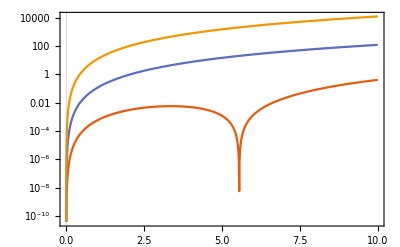

```mathematica
LogPlot[{SNR[t,10,0.25,2*π*0.01,0.5,0],SNR[t,10,0.025,2*π*0.01,5,0],SNR[t,10,0.0025,2*π*0.01,50,0]},{t,0,10},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotTheme->"Scientific"]
```

Save data

```mathematica
SNR1=Table[Re[SNR[10*i/1000,10,0.25,2*π*0.01,0.5,0]],{i,1,1000}];
Export["SNR1.csv",SNR1];
```

```mathematica
SNR2=Table[Re[SNR[10*i/1000,10,0.025,2*π*0.01,5,0]],{i,1,1000}];
Export["SNR2.csv",SNR2];
```

```mathematica
SNR3=Table[Re[SNR[10*i/1000,10,0.0025,2*π*0.01,50,0]],{i,1,1000}];
Export["SNR3.csv",SNR3];
```

```mathematica
SNR1=Table[Re[SNR[10/1000*i,10,0.25,2*π*0.01*(1+RandomReal[{-0.2,0.2}]),0.5,0]],{i,1,1000},{j,1,1000}];
Export["SNR1_RobustnesFreq.csv",SNR1];
```

```mathematica
SNR2=Table[Re[SNR[10/1000*i,10,0.025,2*π*0.01*(1+RandomReal[{-0.2,0.2}]),5,0]],{i,1,1000},{j,1,1000}];
Export["SNR2_RobustnesFreq.csv",SNR2];
```

```mathematica
SNR3=Table[Re[SNR[10/1000*i,10,0.0025,2*π*0.01*(1+RandomReal[{-0.2,0.2}]),50,0]],{i,1,1000},{j,1,1000}];
Export["SNR3_RobustnesFreq.csv",SNR3];
```

```mathematica
Directory[]
```

C:\Users\Mo Zhou\Documents

```mathematica
SNR1=Table[Re[SNR[10/1000*i,10,0.25*(1+RandomReal[{-0.2,0.2}]),2*π*0.01,0.5,0]],{i,1,1000},{j,1,1000}];
Export["SNR1_RobustnesKai.csv",SNR1];
```

```mathematica
SNR2=Table[Re[SNR[10/1000*i,10,0.025*(1+RandomReal[{-0.2,0.2}]),2*π*0.01,5,0]],{i,1,1000},{j,1,1000}];
Export["SNR2_RobustnesKai.csv",SNR2];
```

```mathematica
SNR3=Table[Re[SNR[10/1000*i,10,0.0025*(1+RandomReal[{-0.2,0.2}]),2*π*0.01,50,0]],{i,1,1000},{j,1,1000}];
Export["SNR3_RobustnesKai.csv",SNR3];
```

```mathematica
N[1/(2π)]
```

0.159155

```mathematica
D[x[t],t]-ω*x[t]-b*a[t]==0
```

-b a[t]-ω x[t]+x'[t]==0

```mathematica
DSolve[{-a[t]-I*ω x[t]-κ/2*x[t]+x'[t]==0,x[0]==a0},{x[t]},{t}]
```

{{x[t]→ⅇ^((t κ)/2+ⅈ t ω) (a0+ⅇ^(-1/2 κ K[1]-ⅈ ω K[1]) a[K[1]]K[1]0t)}}